```mathematica
Quit
(* DEFINITIONS, needed *)
```

```mathematica
NN=24;                                                                                                   (* defines number of fermions, use even numbers, can do up to NN = 26 locally, J=1*)
```

```mathematica
(* BUILDING THE GAMMA MATRICES, needed *)
AbsoluteTiming[
SetSharedVariable[gamma,sy,sz,sx,NN,id]
SetSharedFunction[fkpx,fkpid]

sx=SparseArray[{{0,1.},{1.,0}}];sy=SparseArray[{{0.,-ⅈ},{ⅈ,0}}];sz=SparseArray[{{1.,0},{0,-1}}];id=SparseArray[{{1.,0},{0,1}}];

gamma=SparseArray[Table[0,{i,1,NN},{j,1,2^(NN/2)},{k,1,2^(NN/2)}]];
fkpx[x_]:=KroneckerProduct[x,sx];
fkpid[x_]:=KroneckerProduct[x,id];

ParallelDo[gamma[[2m]]=1/Sqrt[2]KroneckerProduct[Nest[fkpx,sx,NN/2-m-1],sy,Nest[fkpid,id,m-2]];gamma[[2m+1]]=1/Sqrt[2]KroneckerProduct[Nest[fkpx,sx,NN/2-m-1],sz,Nest[fkpid,id,m-2]], {m,2,NN/2-1}]

gamma[[1]]=1/Sqrt[2]Nest[fkpx,sx,NN/2-1];
gamma[[2]]=1/Sqrt[2]KroneckerProduct[Nest[fkpx,sx,NN/2-2],sy];
gamma[[3]]=1/Sqrt[2]KroneckerProduct[Nest[fkpx,sx,NN/2-2],sz];
gamma[[NN]]=1/Sqrt[2]KroneckerProduct[sy,Nest[fkpid,id,NN/2-2]];

ParallelDo[gamma[[i]]=SparseArray[gamma[[i]]], {i,1,NN}];]
```

{28.5465,Null}

```mathematica
(* Not parallel *)
AbsoluteTiming[
sx=SparseArray[{{0,1.},{1.,0}}];sy=SparseArray[{{0.,-ⅈ},{ⅈ,0}}];sz=SparseArray[{{1.,0},{0,-1}}];id=SparseArray[{{1.,0},{0,1}}];

gamma=SparseArray[Table[0,{i,1,NN},{j,1,2^(NN/2)},{k,1,2^(NN/2)}]];
fkpx[x_]:=KroneckerProduct[x,sx];
fkpid[x_]:=KroneckerProduct[x,id];

Do[gamma[[2m]]=1/Sqrt[2]KroneckerProduct[Nest[fkpx,sx,NN/2-m-1],sy,Nest[fkpid,id,m-2]];gamma[[2m+1]]=1/Sqrt[2]KroneckerProduct[Nest[fkpx,sx,NN/2-m-1],sz,Nest[fkpid,id,m-2]], {m,2,NN/2-1}]

gamma[[1]]=1/Sqrt[2]Nest[fkpx,sx,NN/2-1];
gamma[[2]]=1/Sqrt[2]KroneckerProduct[Nest[fkpx,sx,NN/2-2],sy];
gamma[[3]]=1/Sqrt[2]KroneckerProduct[Nest[fkpx,sx,NN/2-2],sz];
gamma[[NN]]=1/Sqrt[2]KroneckerProduct[sy,Nest[fkpid,id,NN/2-2]];

Do[gamma[[i]]=SparseArray[gamma[[i]]], {i,1,NN}];]
```

{27.0288,Null}

```mathematica
(* SYK HAMILTONIAN, can be replace by loading a saved Hamiltonian, needed *)

idd=SparseArray[Table[KroneckerDelta[j,k],{j,1,2^(NN/2)},{k,1,2^(NN/2)}]];
SetSharedVariable[H]
H=Table[0,{j,1,2^(NN/2)},{k,1,2^(NN/2)}];

Do[H=H+RandomVariate[NormalDistribution[0,Sqrt[3!/NN^3]]]gamma[[i]].gamma[[j]].gamma[[k]].gamma[[l]],{i,1,NN-3},{j,i+1,NN-2}, {k,j+1,NN-1},{l,k+1,NN}];

(* EIGENVALUES, needed *)

Eigensystem[H+20idd][[2]]//Chop;
d=Transpose[%];
evalues=Eigenvalues[H+20idd]-20//Chop;
lambda=Conjugate[Transpose[d]].H.d//Chop;
                                                                                                         


(* CONSTRUCTING STATE *)

n=Length[evalues];
psi0d=Table[0,{i,1, n}];
wlow=0.90*evalues[[n]];
whigh=0.80*evalues[[n]];                                  (* wlow and whigh set a window from which to selected e-states, must be tuned *)

Do[psi0d[[i]]=UnitStep[whigh-evalues[[i]]]UnitStep[evalues[[i]]-wlow](Random[]+I Random []),{i,1,n}];
psi0dn=psi0d/Sqrt[Conjugate[psi0d].psi0d];
psi0=d.psi0dn;

energy=Re[Conjugate[psi0dn].lambda.psi0dn];

Clear[beta]
z=Tr[MatrixExp[-beta lambda]];
ebeta=-1/z D[z,beta];
F=-Log[z]/beta;
S=beta*(ebeta-F);
FindRoot[ebeta==energy,{beta,100}];


beta=%[[1,2]]//Chop;
tscram= beta Log[S]/(2 Pi);
```

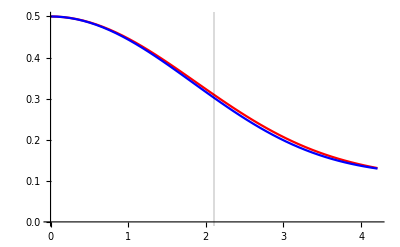

```mathematica
(* TWO POINT FUNCTION, needed *)

psi1d=ConjugateTranspose[d].gamma[[1]].d;
psi1[t_]:=d.MatrixExp[I t lambda].psi1d.MatrixExp[-I t lambda].ConjugateTranspose[d];


tmax= 2 tscram;
tstep = tmax/50;
tmin = 0;

twopointpure=Table[Conjugate[psi0].psi1[i].gamma[[1]].psi0//Chop,{i,tmin,tmax,tstep}];
twopointthermal=Table[Tr[d.MatrixExp[-beta lambda].Conjugate[Transpose[d]].psi1[i].gamma[[1]]]//Chop, {i,tmin,tmax,tstep}]/Tr[MatrixExp[-beta lambda]];
ListPlot[{Re[twopointpure],Re[twopointthermal]}, Joined->True, PlotStyle->{Red, Blue},DataRange->{tmin,tmax},GridLines->{{{tscram,Black}}, None}]
```

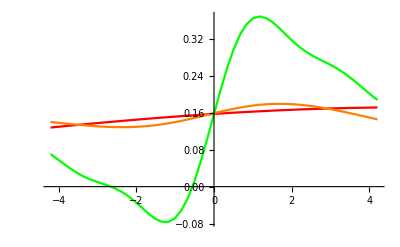

```mathematica
(* ONE POINT FUNCTION *)

tf=0;
a=0.5;
tmax4=tscram*4;
tstep4 = tmax4/25;

b=ⅈ a psi1[tf];

psi0int = MatrixExp[-beta H/2].MatrixExp[b].MatrixExp[beta H/2].psi0;
psi0intn = psi0int/Sqrt[Conjugate[psi0int].psi0int];

psi0ext = MatrixExp[b].psi0;
psi0extn = psi0ext/Sqrt[Conjugate[psi0ext].psi0ext];


onepointpure=Table[Conjugate[psi0].psi1[i].psi0//Chop,{i,-tmax4,tmax4,tstep4}];
onepointext=Table[Conjugate[psi0extn].psi1[i].psi0extn//Chop,{i,-tmax4,tmax4,tstep4}];
onepointint=Table[Conjugate[psi0intn].psi1[i].psi0intn//Chop,{i,-tmax4,tmax4,tstep4}];
ListPlot[{Re[onepointpure],Re[onepointext], Re[onepointint]}, Joined->True, PlotStyle->{Red, Green, Orange},DataRange->{-tmax,tmax},PlotRange->Full]
```

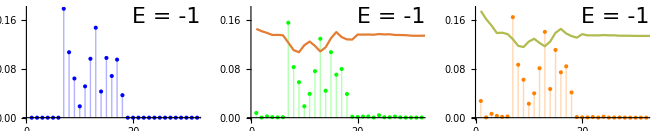

```mathematica
(* DENSITY OF STATES, needs previous parts*)

espure = Reverse[Abs[ConjugateTranspose[d].psi0]^2];
esext = Reverse[Abs[ConjugateTranspose[d].psi0extn]^2];
esint = Reverse[Abs[ConjugateTranspose[d].psi0intn]^2];

Epure = energy;
Eext = Re[Conjugate[psi0extn].H.psi0extn];
Eint = Re[Conjugate[psi0intn].H.psi0intn];

Tepure = StringJoin["E = ",TextString[NumberForm[energy,5]]];
Teext = StringJoin["E = ",TextString[NumberForm[Eext,5]]];
Teint= StringJoin["E = ",TextString[NumberForm[Eint,5]]];

bin=Max[2^(NN/2-9),1];
nbin=Min[512,n];
binrange=nbin/8;
smear=1*bin;

bespure = Table[Sum[espure[[i+(j-1)*bin]],{i,1,bin}],{j,1,nbin}];
besext= Table[Sum[esext[[i+(j-1)*bin]],{i,1,bin}],{j,1,nbin}];
besint = Table[Sum[esint[[i+(j-1)*bin]],{i,1,bin}],{j,1,nbin}];

rmax=Max[bespure];

hespure = Table[ Sum[espure[[Max[i+(j-1),1]]],{i,-smear,smear}]/smear/2,{j,1,nbin-smear,bin}];
hesext= Table[ Sum[esext[[Max[i+(j-1),1]]],{i,-smear,smear}]/smear/2,{j,1,nbin-smear,bin}];
hesint = Table[ Sum[esint[[Max[i+(j-1),1]]],{i,-smear,smear}]/smear/2,{j,1,nbin-smear,bin}];

nnl=Length[hesext];

jesext = (hesext-hespure)+1.5*rmax/2;
jesext[[nnl]] =3.*rmax/8;
jesext[[nnl-1]] = 4.6*rmax/8;


jesint = (hesint - hespure) +1.5*rmax/2;
jesint[[nnl]] =3.*rmax/8;
jesint[[nnl-1]] = 4.6*rmax/8;


s1=ListPlot[bespure,Filling->Axis,PlotRange->{{0,binrange},{0,rmax}},PlotStyle->{Blue,Thick},Ticks->False, Epilog->{Text[Style[Tepure,22],Scaled[{1,1}],{1,1}]}];
s2=ListPlot[besext,Filling->Axis,PlotRange->{{0,binrange},{0,rmax}},PlotStyle->{Green,Thick},Ticks->False, Epilog->{Text[Style[Teext, 22],Scaled[{1,1}],{1,1}]}];
s3=ListPlot[besint,Filling->Axis,PlotRange->{{0,binrange},{0,rmax}},PlotStyle->{Orange,Thick},Ticks->False, Epilog->{Text[Style[Teint, 22],Scaled[{1,1}],{1,1}]}];


h2=ListPlot[jesext,Joined->True,PlotRange->{{0,binrange/smear*2},Full},ColorFunction->"Rainbow",Ticks->False];
h3=ListPlot[jesint,Joined->True,PlotRange->{{0,binrange/smear*2},Full},ColorFunction->"Rainbow",Ticks->False];

GraphicsRow[{s1,Show[s2,h2],Show[s3,h3]}]
```

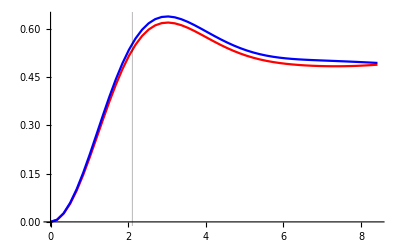

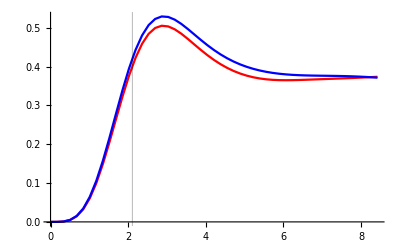

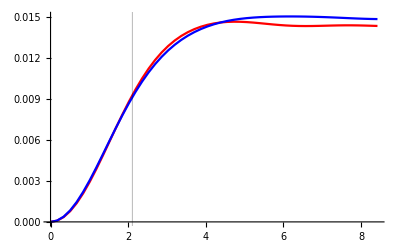

```mathematica
(* OTOC and BEYOND, Probing four point functions, needs previous parts*)

tmax2 =2*tmax;
tstep2 = tmax2/50;

point4pure=Table[Conjugate[psi0].-MatrixPower[psi1[i].gamma[[1]]-gamma[[1]].psi1[i],2].psi0//Chop,{i,tmin,tmax2,tstep2}];
point4thermal=Table[Tr[d.MatrixExp[-beta lambda].Conjugate[Transpose[d]].-MatrixPower[psi1[i].gamma[[1]]-gamma[[1]].psi1[i],2]]//Chop, {i,tmin,tmax2,tstep2}]/Tr[MatrixExp[-beta lambda]];
ListPlot[{Re[point4pure],Re[point4thermal]}, Joined->True, PlotStyle->{Red, Blue},DataRange->{tmin,tmax2},GridLines->{{{tscram,Black}}, None}]

point8pure=Table[Conjugate[psi0].MatrixPower[psi1[i].gamma[[1]]-gamma[[1]].psi1[i],4].psi0//Chop,{i,tmin,tmax2,tstep2}];
point8thermal=Table[Tr[d.MatrixExp[-beta lambda].Conjugate[Transpose[d]].MatrixPower[psi1[i].gamma[[1]]-gamma[[1]].psi1[i],4]]//Chop, {i,tmin,tmax2,tstep2}]/Tr[MatrixExp[-beta lambda]];
ListPlot[{Re[point8pure],Re[point8thermal]}, Joined->True, PlotStyle->{Red, Blue},DataRange->{tmin,tmax2},GridLines->{{{tscram,Black}}, None}]

gam = gamma[[2]].gamma[[3]].gamma[[4]].gamma[[5]].gamma[[6]].gamma[[7]];

pointMpure=Table[Conjugate[psi0].MatrixPower[psi1[i].gam-gam.psi1[i],2].psi0//Chop,{i,tmin,tmax2,tstep2}];
pointMthermal=Table[Tr[d.MatrixExp[-beta lambda].Conjugate[Transpose[d]].MatrixPower[psi1[i].gam-gam.psi1[i],2]]//Chop, {i,tmin,tmax2,tstep2}]/Tr[MatrixExp[-beta lambda]];
ListPlot[{Re[pointMpure],Re[pointMthermal]}, Joined->True, PlotStyle->{Red, Blue},DataRange->{tmin,tmax2},GridLines->{{{tscram,Black}}, None}]
```

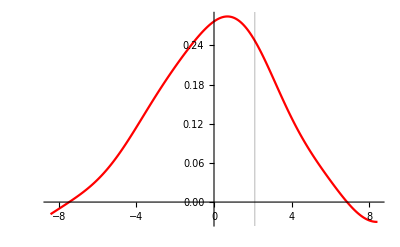

```mathematica
(* Retrieving a particle *)

epsi = 1.5;
g= 1.5;
tf=tscram;

lc = MatrixExp[-beta H/2];
rc = MatrixExp[beta H/2];
gam = psi1[-tf];

psi0ret =( Cos[g]Cos[epsi]+Sin[g]Cos[epsi]gamma[[2]].lc.gamma[[2]].rc+ⅈ Cos[g]Sin[epsi] lc.gam.rc - ⅈ Sin[g]Sin[epsi]gamma[[2]].lc.gam.gamma[[2]].rc).psi0;


psi0retn = psi0ret/Sqrt[Conjugate[psi0ret].psi0ret];


retrieve=Table[Conjugate[psi0retn].psi1[i].psi0retn//Chop,{i,-tmax2,tmax2,tstep}];
ListPlot[{Re[retrieve]}, Joined->True, PlotStyle->{Red},DataRange->{-tmax2,tmax4},PlotRange->Full,GridLines->{{{tscram,Black}}, None}]
```